# Accuracy and Numerical Stability

We have seen a number of Numerical ODE solvers so far.  We have the BDF family, we have the Taylor series family, we have Pade generalizations of Taylor series solvers, and we have two old favorites (Implicit and Explicit Euler) and a few others that are the simplest cases of several families.

The hope is that fancier solvers will let us maintain accuracy with larger steps.  We restrict attention to autonomous ODE systems y'=f(y) on ℝ^n with f(0)=y_0∈ℝ^n and assume that f is as smooth as is required for our computations.

## Theorems and Definitions.

### Smoothness

If y'=f(y) and f(0)=x  then 
	y''=Df(y).y'  and J'=Df(y).J(y) with J(0)=I_n
where Df:ℝ^n→ℝ^(n×n) is the Jacobian matrix and J(t)=∇_x y(t) is the gradient of the solutions with respect to the initial condition. This process can be continued to higher derivatives provided f is sufficiently smooth and you are willing to deal with higher order tensors e.g.
	DDf:ℝ^n→ℝ^(n×n×n).
A consequence: 
1) If f is smooth with k continuous derivatives then the solution y is smooth with k+1 derivatives.
2) There is no point in using a numerical solver that relies on smoothness unless the solution is smooth.   
3) Asymptotic error results only apply to smooth problems.

### Stiffness

According to Wikipedia
 https://en.wikipedia.org/wiki/Stiff_equation
“In mathematics, a stiff equation is a differential equation for which certain numerical methods for solving the equation are numerically unstable, unless the step size is taken to be extremely small. It has proven difficult to formulate a precise definition of stiffness, but the main idea is that the equation includes some terms that can lead to rapid variation in the solution.”  
My interpretation “Stiff ODEs are hard!”

According to Cleve Moler
 https://www.mathworks.com/company/technical-articles/stiff-differential-equations.html
“Stiffness is a subtle, difficult, and important - concept in the numerical solution of ordinary differential equations.
…
An ordinary differential equation problem is stiff if the solution being sought is varying slowly, but there are nearby solutions that vary rapidly, so the numerical method must take small steps to obtain satisfactory results.”

What we want are: 
1) Practical tests for stiffness.
2) Practical ode solvers if we suspect stiffness.
3) An understanding of the subtle, difficult, and important concept.

### Stiffness for Linear ODEs: Examples

Example:By any practical definition y'=A.y+f is stiff for almost any initial condition with
	A=(-3.11415×10^9 | 3.14954×10^9 | 3.3947×10^9
3.14954×10^9 | -3.18534×10^9 | -3.43328×10^9
3.3947×10^9 | -3.43328×10^9 | -3.70051×10^9)
and 
	f(t)=sin(t)(0.564388
0.558046
0)
Lets try to understand this claim.   Every part of the solution of y'=A.y decays.

```mathematica
A=({{-3.114149543141176*^9, 3.1495417675676537*^9, 3.394695081544255*^9}, {3.149541767567654*^9, -3.185336226155096*^9, -3.4332757004663835*^9}, {3.3946950815442553*^9, -3.4332757004663835*^9, -3.7005142337037296*^9}});
Eigensystem[A]
```

{{-1.×10^10,-2.,-0.999999},{{0.558046,-0.564388,-0.608319},{0.71872,-0.037676,0.694278},{0.414761,0.82465,-0.384612}}}

### Stiffness Ratio for y'=A.y+g

The solution of y'=A.y with y(0)=y_0 is 
	y(t)=ⅇ^(A t).y_0
where if A is diagonalizable with eigen decomposition A=V.Λ.V^-1 then
	ⅇ^(A t)= V.ⅇ^Λt.V^-1 with ⅇ^(Λ t)=(ⅇ^(λ_1 t) |  |  | 
 | ⅇ^(λ_2 t) |  | 
 |  | ⋱ | 
 |  |  | ⅇ^(λ_n t))
A) If an eigenvalue λ=r is real there is a solution component ~ⅇ^(r t).  
	This component decays if r<0 and decays fast if r<<-1.
	This component grows if r>0 and grows fast if r>>1.
B) If an eigenvalue λ=a±ⅈ b is complex there are solution components ~ⅇ^(a t)cos(b t) and ~ⅇ^(a t)cos(b t)
  	These components decay if a<0 and decays fast if a<<-1.
	These components grow if a>0 and grow fast if a>>1.
	They oscillate rapidly if |b| >> 1
C) Components that decay rapidly compared to others become insignificant after a short period of time.  However, because the ODE is the same there are nearby solutions that would decay rapidly.  Sadly explicit solvers are always ready to react to the fastest time scales in an ODE. 
D) If all the eigenvalues λ_i have Re(λ_i)<0 the ratio of the fastest to the slowest exponential decay rate
	(max_(1≤i≤n) Re(-λ_i))/(min_(1≤i≤n) Re(-λ_i)) 
is the stiffness ratio.   
E) A linear problem is definitely stiff if all eigenvalues have negative real part and the stiffness ratio is large.

### Stiffness for y'=f(y)

The ODE y'=f(y) is definitely stiff at y_0 if all the eigenvalues of Df(y_0) have negative real part and the stiffness ratio is large. The argument is that near y_0 the linearized ODE z'=f(y_0)+Df(y_0).z approximates the behavior of the ODE.

Stiffness is an efficiency problem.  If the stiffness ratio is 10^5 then a non-stiff solver will have to take 10^5 times as many steps as carefully designed stiff solver.

With m=32 the stiffness ratio of the standard 3pt or 5p FD approximation matrix for u_xx is ~500.  The standard ODE  y'=A.y approximations for the heat equation are stiff.  Almost all ODEs that arise from such PDE semi-discretizations are stiff.

```mathematica
m=32; h=π/(m+1);
A3=1/h^2 SparseArray[{Band[{1,1}]->-2.0,Band[{1,2}]->1.0,Band[{2,1}]->1.0},{m,m}];
A5=1/(12 h^2)SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,Band[{3,1}]->-1.0
},{m,m}];
MinMax[Eigenvalues[A3]]
ListLogPlot[Quiet[{Eigenvalues[-A3],Eigenvalues[-A5]}],
PlotLegends->{"-σ(A3)","-σ(A5)"},
PlotMarkers->{"■","•"}]
```

{-440.356,-0.999245}

-Graphics-

### Stiffness for Linear ODEs: Test

A standard test to choose a solver for IVP y'=f(y) with y(0)=y_0 would be to see if the spectrum of 
	A=Df(y_0)
makes the linearized ODE 
	z'=f(y_0)+Df(y_0).z	
stiff. If Re(λ)<0 for all λ∈σ(A) with a large stiffness ratio you (or the software tool) should choose a stiff solver.  Chances are very good that the stiff solver is in or very close to the BDF family.

## What happens if I use a non-stiff solver on a stiff problem?

A non-stiff solver has to take time steps to resolve the fast time scale. If your solver has adaptive time steps it will take tiny steps when there is no obvious reason for tiny time steps. A fixed step solver that does not respect the fast time-scale will produce nonsense.  Here is a simple example.

```mathematica
θ=0.4;R={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
A=R.({{-1, 0}, {0, -10^3}}).Rᵀ; g[t_]:={Cos[1.2t],Sin[1.3 t]}; y0={1.2,3.4}; TMax=123.0;
ySol=NDSolveValue[{y'[t]==A.y[t]+g[t],y[0]==y0},y,{t,0, TMax}];
{tVals}=ySol["Coordinates"];
hVals=Table[tVals⟦i⟧-tVals⟦i-1⟧,{i,2,Length[tVals]}];
TabView[{
"y"->Plot[ySol[t],{t,0,TMax},PlotRange->All],
"y_Start"->Plot[ySol[t],{t,0,0.1},PlotRange->All],
"h"->ListLogPlot[hVals]}]
```

123

Lets see what happens if I try to use a fixed step size Euler method.   We are going to start small.

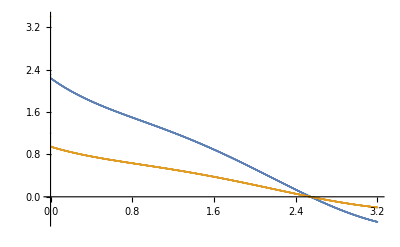

```mathematica
f[t_,y_]:=A.y+g[t]
EulerStep[f_,h_][{t_,y_}]:= {t+h,y+h f[t,y]}
TMax=3.2;
n=3000;
h=TMax/n;
EulerData=NestList[EulerStep[f,h],{0,y0},n];
ListPlot[EulerData⟦All,2⟧ᵀ,
DataRange->{0,TMax}]
```

## Instability and stability

The rapidly growing oscillations are symptomatic of taking steps that are too large. Not unreasonably this behavior is called instability.  It can be predicted and explained by looking at the eigenvalues of the linearization matrix individually.

For a diagonalizable m×m matrix A=V.Λ.V^-1 the solution of 
	z'=A.z  with z(0)=z_0 
is easily written down
	z(t)=ⅇ^(A t).z_0=V.ⅇ^(Λ t).V^-1.z_0=V.(ⅇ^(λ_1 t) |   |   |  
  | ⅇ^(λ_2 t) |   |  
  |   | ⋱ |  
  |   |   | ⅇ^(λ_n t)).V^-1.z_0.
The interpretation of this is that the linear problem decouples in the eigenvector basis.
Explicit Euler, Implicit Euler, and Trapezoid schemes for z'=A.z give

Explicit Euler:	z_n=(I+h A)^n.z_0
Implicit Euler:	z_n=(I-h A)^-n.z_0
Trapezoid:	z_n=((I-h/2 A)^-1(I+h/2 A))^n.z_0

Substituting A=V.Λ.V^-1 we get the much simpler expressions
	Explicit Euler: 	(I+h A)^n=V.(I+h Λ)^n.V^-1
	Implicit Euler:	(I-h A)^-n=V.((I-h Λ)^-1)^n.V^-1
	Trapezoid:	((I-h/2 A)^-1(I+h/2 A))^n=V.((I-h/2 Λ)^-1(I+h/2 Λ))^n.V^-1
If all the modes decay then the real part of every eigenvalue λ is negative.  If the system is stiff then some of the eigenvalues are well to the left in the left half complex plane.  The inner pieces are
	Explicit Euler: 	(1+h λ_1 |   |   |   
  | 1+h λ_2 |   |  
  |   | ⋱ |  
  |   |   | 1+h λ_m)^n=((1+h λ_1)^n |   |   |   
  | (1+h λ_2)^n |   |  
  |   | ⋱ |  
  |   |   | (1+h λ_m)^n)
	Implicit Euler:	(1/(1-h λ_1) |   |   |   
  | 1/(1-h λ_2) |   |  
  |   | ⋱ |  
  |   |   | 1/(1-h λ_m))^n=((1/(1- h λ_1))^n |   |   |   
  | (1/(1- h λ_2))^n |   |  
  |   | ⋱ |  
  |   |   | (1/(1- h λ_m))^n)
	Trapezoid:	((1+ h/2 λ_1)/(1-h/2 λ_1) |   |   |   
  | (1+h/2 λ_2)/(1-h/2 λ_2) |   |  
  |   | ⋱ |  
  |   |   | (1+h/2 λ_m)/(1-h/2 λ_m))^n=(((1+ h /2 λ_1)/(1- h /2 λ_1))^n |   |   |   
  | ((1 + h /2 λ_2)/(1- h /2 λ_2))^n |   |  
  |   | ⋱ |  
  |   |   | ((1 + h /2 λ_m)/(1- h /2 λ_m))^n)

Note: Everything is in terms of the scaled variables z=h λ_i.  We have 
	Explicit Euler: 	→r_ee(z)=1+z
	Implicit Euler:	→r_ie(z)=1/(1-z)
	Trapezoid:	→r_t(z)=(1 + z/2)/(1 - z/2)
These are the stability functions of these simple single step schemes.

Once we understand that the modes decouple we can define the stability function simply as the result of applying a step of the numerical scheme to the scalar Dahlquist test problem
	y'=λ y
to get r(λ h)y(0).  If Re[λ]<0 then the analytic solution ⅇ^(λ t)y(0) decays as t→∞.  A numerical method that does not reproduce this decay is useless!  Applying any one of the three solvers above to the test problem gives (r(λ h))^n y(0) which decays provided |r(λ h)|<1.   The stability region of a single step solver is the region in the complex plane where |r(z)|<1.

```mathematica
TabView[{
"Explicit Euler"->RegionPlot[Abs[1+x+I y]<1,{x,-3,3},{y,-3,3},GridLines->Automatic],
"Implicit Euler"->RegionPlot[Abs[1/(1-(x + I y))]<1,{x,-3,3},{y,-3,3},GridLines->Automatic],
"Trap"->RegionPlot[Abs[(1 + 0.5 (x+I y))/(1-0.5(x + I y))]<1,{x,-3,3},{y,-3,3},GridLines->Automatic]
}]
```

123

An alternative (and frequently a more efficient) way to plot the boundary is to solve r(z)=ⅇ^(ⅈ θ) for z.   Explicit Euler approximations decay provided z=λ h is inside the circle radius 1 centered at the origin.   Implicit Euler and Trapezoid approximations decay (as they should) whenever z=λ h is in the left half plane where the analytic solution decays.

Analytic solutions decay when the eigenvalues are in the left half plane.  Numerical schemes that decay regardless of step size h when the analytic solution decays are A Stable .

Note: Stability has almost nothing to do with accuracy!

## Global Accuracy

Approximations for advancing y'=λ y from y(0)=1 to y(1)=ⅇ^λ with n steps of size h=1/n are
	Explicit Euler: 	y_ee=(1+λ/n)^n y(0)
	Implicit Euler:	y_ie=(1/(1-λ/n))^ny(0)
	Trapezoid:	y_t=((1 + λ/(2n))/(1 - λ/(2n)))^ny(0)
We can see plot the relative global accuracy as a function of λ∈ℂ and n∈ℤ^+

```mathematica
n=22;
TabView[{
"Explicit Euler"->ComplexPlot3D[1-(1+λ/n)^n/E^λ,{λ,1},
PlotLegends->Automatic],
"Implicit Euler"->ComplexPlot3D[1-1/(E^λ (1-λ/n)^n),{λ,1},
PlotLegends->Automatic],
"Trapezoid"->ComplexPlot3D[1-(1+0.5λ/n)^n/(E^λ (1-0.5λ/n)^n),{λ,1},
PlotLegends->Automatic]
}]
```

123

## Local Truncation Error and Order

The local truncation error (LTE) for a step of length h for y'=f(t,y) with y(0)=y_0 is 
	y(h)-y_1
where y_1 is the output of the a numerical solver.  We are going to do this for our three solvers. 
Explicit Euler:	y_1=y_0+h f(0,y_0)
Implicit Euler:	y_1=y_0+h f(h,y_1)
Trapezoid:	y_1=y_0+h/2 (f(0,y_0)-f(h,y_1))
As h->0 we hope these all become better approximations to y(h).  The standard way to evaluate how good the formulas are is to substitute the theoretical solution into the LTE and compute the Taylor Series about h=0.
 Explicit Euler LTE:	y(h)-(y_0+h f(0,y_0))
Implicit Euler LTE:	y(h)-(y_0+h f(h,y(h)))
Trapezoid LTE:		y(h)-(y_0+h/2 (f(0,y_0)-f(h,y(h)))
We need to remember that y(0)=y_0 and y'(0)=f(0,y_0) and y''(0)=∂_t f(0,y_0)+∇_y f(0,y_0).y'(0) and …

```mathematica
Series[y[h]-(y0+h f[0,y0]),{h,0,2}]
Series[y[h]-(y0+h f[0,y0]),{h,0,2}]/.{y[0]->y0,y'[0]->f[0,y0]}
```

(-y0+y[0])+(-f[0,y0]+y'[0]) h+1/2 y''[0] h^2+O[h]^3

1/2 y''[0] h^2+O[h]^3

```mathematica
Series[y[h]-(y[0]+h f[h,y[h]]),{h,0,2}]
Simplify[Series[y[h]-(y[0]+h f[h,y[h]]),{h,0,2}]//.{
y[0]->y0,y'[0]->f[0,y0],
y''[0]->+Derivative[1,0][f][0,y0]+ Derivative[0,1][f][0,y0]y'[0]}]
```

(-f[0,y[0]]+y'[0]) h+(y''[0]/2-y'[0] f^(0,1)[0,y[0]]-f^(1,0)[0,y[0]]) h^2+O[h]^3

(-1/2 f[0,y0] f^(0,1)[0,y0]-1/2 f^(1,0)[0,y0]) h^2+O[h]^3

```mathematica
Series[y[h]-(y0+h/2( f[0,y[h]]+f[h,y[h]])),{h,0,2}]
Simplify[Series[y[h]-(y0+h/2( f[0,y[h]]+f[h,y[h]])),{h,0,3}]//.{
y[0]->y0,y'[0]->f[0,y0],
y''[0]->+Derivative[1,0][f][0,y0]+ Derivative[0,1][f][0,y0]y'[0]}]
```

(-y0+y[0])+(-f[0,y[0]]+y'[0]) h+1/2 (y''[0]-2 y'[0] f^(0,1)[0,y[0]]-f^(1,0)[0,y[0]]) h^2+O[h]^3

-1/2 (f[0,y0] f^(0,1)[0,y0]) h^2+1/12 (2 y^(3)[0]-6 f[0,y0]^2 f^(0,2)[0,y0]-6 f^(0,1)[0,y0] f^(1,0)[0,y0]-6 f[0,y0] ((f^(0,1)[0,y0])^2+f^(1,1)[0,y0])-3 f^(2,0)[0,y0]) h^3+O[h]^4

In practice ODE solvers control the local “one-step” error and make sure that errors do not amplify.